```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω0+ⅈ κ1, κ}, {κ, ω1+ⅈ κ2}});
ωS=Eigenvalues[Ω][[1]]
ωAS=Eigenvalues[Ω][[2]]
```

1/2 (ⅈ κ1+ⅈ κ2+ω0+ω1-√((-ⅈ κ1-ⅈ κ2-ω0-ω1)^2-4 (-κ^2-κ1 κ2+ⅈ κ2 ω0+ⅈ κ1 ω1+ω0 ω1)))

1/2 (ⅈ κ1+ⅈ κ2+ω0+ω1+√((-ⅈ κ1-ⅈ κ2-ω0-ω1)^2-4 (-κ^2-κ1 κ2+ⅈ κ2 ω0+ⅈ κ1 ω1+ω0 ω1)))

```mathematica
rnum={ω0-> 1.0,ω1-> 1.0,κ-> 0.05};
Print[{ωbAS, ωbC, ωbS}/.rnum]
```

{ωbAS,ωbC,ωbS}

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"Uncoupled frequency deviation (GHz)","Relative frequency (GHz)"}}];
```

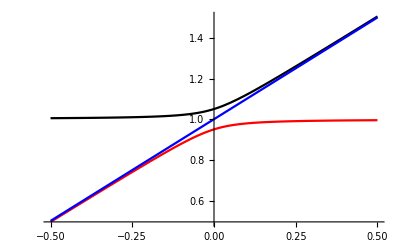

```mathematica
rnum={ω0-> 1.0+δ,ω1-> 1.0,κ-> 0.05,κ1-> 0.1,κ2->0.1};
Plot[{Re@ωS,Re@ωAS, ω0}/.rnum//Evaluate,{δ,-0.5,0.5},PlotStyle->{Red,Black,Blue, Gray}](*,{Gray,Dashed}}]*)
```

General::munfl: Exp[-2065.27] is too small to represent as a normalized machine number; precision may be lost.

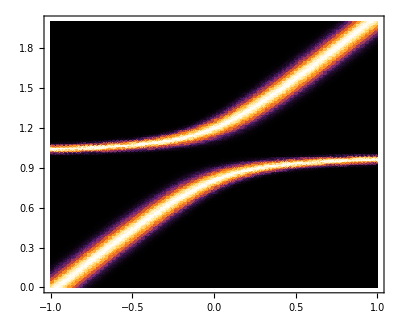

```mathematica
rnum={ω0-> 1.0+δ,ω1-> 1.0,κ-> 0.2,κ1-> 0.1,κ2->0.02};
DensityPlot[{Exp[-((ω-Re@ωS)/(Im@ωS))^2]+Exp[-((ω-Re@ωAS)/(Im@ωAS))^2]}/.rnum//Evaluate,{δ,-1,1},{ω,0,2},PlotRange->All,PlotPoints->80,ColorFunction->ColorData["SunsetColors"],AspectRatio->0.8]
```

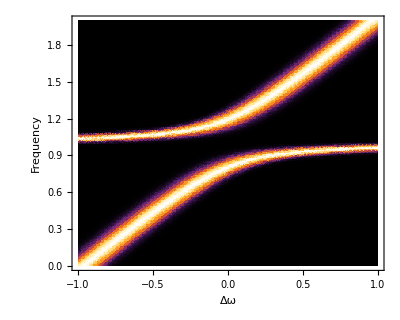

```mathematica
Show[%,FrameLabel->{"Δω","Frequency"},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}]
```

```mathematica
λ0=1.55 10^-6;
ν0=(3 10^8)/λ0/10^9;
```

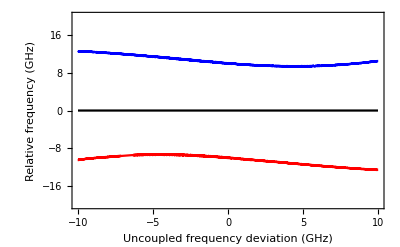

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"Uncoupled frequency deviation (GHz)","Relative frequency (GHz)"}}];
rnum={ω0-> ν0+δ,ω1-> ν0,ω2-> ν0,κ-> 10/Sqrt[2]};
Plot[{ωbAS-ωbC,ωbC-ωbC,ωbS-ωbC}/.rnum//Evaluate,{δ,-10,10},PlotStyle->{Red,Black,Blue}, PlotRange->{{-10, 10},{-20, 20}}]
```

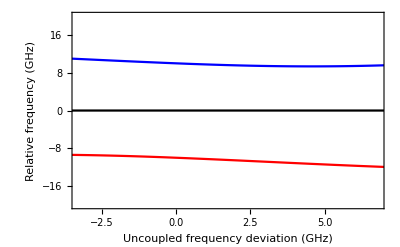

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"Uncoupled frequency deviation (GHz)","Relative frequency (GHz)"}}];
rnum={ω0-> 0+δ,ω1-> 0,ω2-> 0,κ-> 10/Sqrt[2]};
Relativefreq = Plot[{ωbAS-ωbC,ωbC-ωbC,ωbS-ωbC}/.rnum//Evaluate,{δ,-20,20},PlotStyle->{Red,Black,Blue}, PlotRange->{{-3.3, 6.8},{-20, 20}}]
```

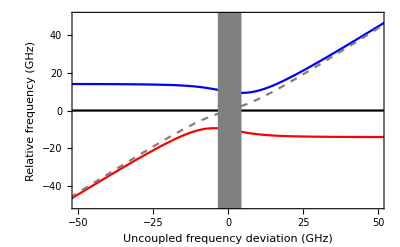

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"Uncoupled frequency deviation (GHz)","Relative frequency (GHz)"}}];
rnum={ω0-> 0+δ,ω1-> 0,ω2-> 0,κ-> 10/Sqrt[2]};
Relativefreq = Plot[{ωbAS-ωbC,ωbC-ωbC,ωbS-ωbC, ω0-ωbC}/.rnum//Evaluate,{δ,-100,100},PlotStyle->{Red,Black,Blue, {Gray, Dashed}}, PlotRange->{{-50, 50},{-50, 50}}];
Highlight = Graphics[{Gray, Rectangle[{-3.4,-100},{4.5,100}]}];
Show[Relativefreq, Highlight]
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\Anticrossing.pdf",%38,"PDF"]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\Anticrossing.pdf

```mathematica
(*Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\Anticrossing.pdf",%112,"PDF"]*)
```

```mathematica
(*Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\Anticrossing.pdf",%60,"PDF"]*)
```

```mathematica
(*Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\Anticrossing.pdf", Relativefreq, Highlight]*)
```

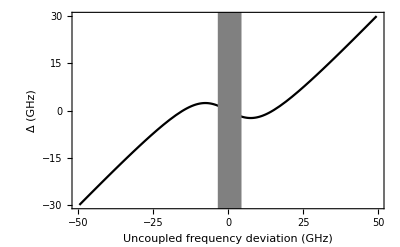

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"Uncoupled frequency deviation (GHz)","Δ (GHz)"}}];
LocalDispersion = Plot[{ωbS-ωbC - (ωbC-ωbAS)}/.rnum//Evaluate,{δ,-50, 50},PlotStyle->Black, PlotRange->{{-50, 50},{-30, 30}}]; (*PlotRange->{{-10,5},{-2, 1}}]*)
Show[LocalDispersion, Highlight]
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\LocalDispersion Mathematica.pdf",%31,"PDF"]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\LocalDispersion Mathematica.pdf

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\LocalDispersion Mathematica.pdf",%42,"PDF"]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\LocalDispersion Mathematica.pdf

```mathematica
(*Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\LocalDispersion Mathematica.pdf",%126,"PDF"]*)
```

```mathematica
(*Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\LocalDispersion Mathematica.pdf", LocalDispersion]*)
```

```mathematica
Delta = Table[ωbS-ωbC - (ωbC-ωbAS)/.rnum//Evaluate, {δ,-100, 100, 0.1}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\processing\\Delta model.csv", Delta]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\processing\Delta model.csv

```mathematica
Srelative = Table[ωbS-ωbC/.rnum//Evaluate, {δ,-100, 100, 0.1}];
Crelative = Table[ωbC-ωbC/.rnum//Evaluate, {δ,-100, 100, 0.1}];
ASrelative = Table[ωbAS-ωbC/.rnum//Evaluate, {δ,-100, 100, 0.1}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\processing\\Symmetric relative freq_model.csv", Srelative];
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\processing\\Central relative freq_model.csv", Crelative];
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\processing\\Anti-symmetric relative freq_model.csv", ASrelative];
```

```mathematica
freqdeviation= Table[δ, {δ,-100, 100, 0.1}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\Papers\\Journals\\2024 - Nathalia - DOPO in photonic molecules\\Figures\\processing\\freqdeviation_model.csv", freqdeviation];
```

```mathematica
ClearAll[κ,ω0,ω1,ω2,ω3,Ω]
Ω=({{ω0+δ, κ, 0}, {κ, ω1, κ}, {0, κ, ω2}});
ωbAS=Eigenvalues[Ω][[1]]
ωbC=Eigenvalues[Ω][[2]]
ωbS=Eigenvalues[Ω][[3]]
```

Root[δ κ^2+κ^2 ω0+κ^2 ω2-δ ω1 ω2-ω0 ω1 ω2+(-2 κ^2+δ ω1+ω0 ω1+δ ω2+ω0 ω2+ω1 ω2) #1+(-δ-ω0-ω1-ω2) #1^2+#1^3&,1]

Root[δ κ^2+κ^2 ω0+κ^2 ω2-δ ω1 ω2-ω0 ω1 ω2+(-2 κ^2+δ ω1+ω0 ω1+δ ω2+ω0 ω2+ω1 ω2) #1+(-δ-ω0-ω1-ω2) #1^2+#1^3&,2]

Root[δ κ^2+κ^2 ω0+κ^2 ω2-δ ω1 ω2-ω0 ω1 ω2+(-2 κ^2+δ ω1+ω0 ω1+δ ω2+ω0 ω2+ω1 ω2) #1+(-δ-ω0-ω1-ω2) #1^2+#1^3&,3]

```mathematica
NSolve[{A*25^2+B==-3.3, A*32^2+B==6.8}, {A,B}]
```

{{A→0.0253133,B→-19.1208}}